```mathematica
trueCheck=0;
schoolbook[A_,B_]:=
Block[
{C,i,j,k,n},
n=Length[A];
C=Table[Table[0,{j,1,n}],{i,1,n}];
For[
i=1,i≤n,i++,
For[
j=1,j≤n,j++,
For[
k=1,k≤n,k++,
C[[i]][[j]]=C[[i]][[j]]+A[[i]][[k]]*B[[k]][[j]]
]
]
];
Return[C]
];
newAlgoV1[A_,B_]:=
Block[
{Cr,n,a,b,c,d,e,f,g,h,λ,k1,k2,k3,k4,Ap,Bp,i,j,C1,C2,C3,C4},
n=Length[A];
If[
n==1, 
λ=ToExpression[StringJoin["x",ToString[trueCheck]]];
Return[{{Collect[A[[1]][[1]]*B[[1]][[1]],λ]}}]
,
Cr=Table[Table[0,{i,1,n}],{j,1,n}];
a=Table[Table[A[[i]][[j]],{j,1,n/2}],{i,1,n/2}];
b=Table[Table[A[[i]][[j]],{j,n/2+1,n}],{i,1,n/2}];
c=Table[Table[A[[i]][[j]],{j,1,n/2}],{i,n/2+1,n}];
d=Table[Table[A[[i]][[j]],{j,n/2+1,n}],{i,n/2+1,n}];
e=Table[Table[B[[i]][[j]],{j,1,n/2}],{i,1,n/2}];
f=Table[Table[B[[i]][[j]],{j,n/2+1,n}],{i,1,n/2}];
g=Table[Table[B[[i]][[j]],{j,1,n/2}],{i,n/2+1,n}];
h=Table[Table[B[[i]][[j]],{j,n/2+1,n}],{i,n/2+1,n}];
trueCheck=trueCheck+1;
λ=ToExpression[StringJoin["x",ToString[trueCheck]]];
k1=Table[Table[a[[i]][[j]]+λ^2c[[i]][[j]],{j,1,n/2}],{i,1,n/2}];
k2=Table[Table[e[[i]][[j]]+λ f[[i]][[j]],{j,1,n/2}],{i,1,n/2}];
k3=Table[Table[b[[i]][[j]]+λ^2d[[i]][[j]],{j,1,n/2}],{i,1,n/2}];
k4=Table[Table[g[[i]][[j]]+λ h[[i]][[j]],{j,1,n/2}],{i,1,n/2}];
Ap=newAlgoV1[k1,k2];
Bp=newAlgoV1[k3,k4];C1=Table[Table[ Coefficient[Ap[[i]][[j]],λ,0]+Coefficient[Bp[[i]][[j]],λ,0],{j,1,n/2}],{i,1,n/2}];
C2=Table[Table[ Coefficient[Ap[[i]][[j]],λ,1]+Coefficient[Bp[[i]][[j]],λ,1],{j,1,n/2}],{i,1,n/2}];
C3=Table[Table[ Coefficient[Ap[[i]][[j]],λ,2]+Coefficient[Bp[[i]][[j]],λ,2],{j,1,n/2}],{i,1,n/2}];
C4=Table[Table[ Coefficient[Ap[[i]][[j]],λ,3]+Coefficient[Bp[[i]][[j]],λ,3],{j,1,n/2}],{i,1,n/2}];
For[
i=1,i≤n,i++,
For[
j=1,j≤n,j++,
If[i≤n/2&&j≤n/2,Cr[[i]][[j]]=C1[[i]][[j]]];
If[i≤n/2&&j>n/2,Cr[[i]][[j]]=C2[[i]][[j-n/2]]];
If[i>n/2&&j≤n/2,Cr[[i]][[j]]=C3[[i-n/2]][[j]]];
If[i>n/2&&j>n/2,Cr[[i]][[j]]=C4[[i-n/2]][[j-n/2]]];
]
];
Return[Cr]
]
];
newAlgo[A_,B_]:=Block[{},trueCheck=0; Return[newAlgoV1[A,B]]];
```

```mathematica
Block[
{A,B,start,end,n},
For[
n=1,n≤128,n=n*2,
Print["Size = ",n];
A=Table[Table[RandomInteger[],{j,1,n}],{i,1,n}];
B=Table[Table[RandomInteger[],{j,1,n}],{i,1,n}];
start=AbsoluteTime[];
schoolbook[A,B];
end=AbsoluteTime[];
Print["Schoolbook algorithm time = ",end-start];
start=AbsoluteTime[];
newAlgo[A,B];
end=AbsoluteTime[]; 
Print["My algorithm time = ",end-start];
]
]
```

Size = 1

Schoolbook algorithm time = 0.000058

My algorithm time = 0.000079

Size = 2

Schoolbook algorithm time = 0.00007

My algorithm time = 0.0003

Size = 4

Schoolbook algorithm time = 0.000483

My algorithm time = 0.00163

Size = 8

Schoolbook algorithm time = 0.00335

My algorithm time = 0.008503

Size = 16

Schoolbook algorithm time = 0.02202

My algorithm time = 0.060726

Size = 32

Schoolbook algorithm time = 0.17932

My algorithm time = 0.20827

Size = 64

Schoolbook algorithm time = 1.14455

My algorithm time = 1.87625

Size = 128

Schoolbook algorithm time = 9.393203

My algorithm time = 11.49505

```mathematica
FindFit[{{1,0.000079},{2,0.000303},{4,0.001628},{8,0.008503},{16,0.060726},{32,0.208269},{64,1.876245},{128,11.495053}},a x^3+b x^2 + c x + d,{a,b,c,d},x]
```

{a→2.95491×10^-6,b→0.000384506,c→-0.00802851,d→0.02705}

```mathematica
Table[2.954905152088621*10^-6*8^i+0.000384506*4^i-0.00802851*2^i+0.02705,{i,1,7}]
```

{0.0125546,0.00127717,-0.0110568,0.00913067,0.260698,1.86277,11.496}

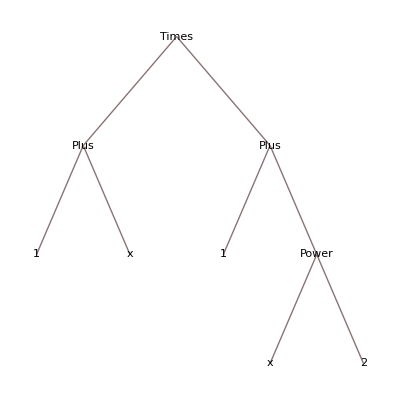

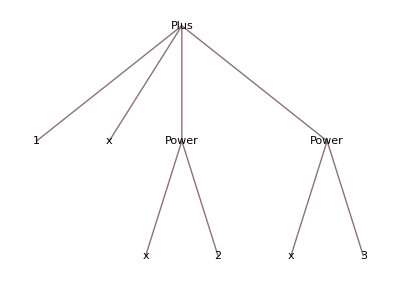

```mathematica
TreeForm[(1+x)(1+x^2)]
TreeForm[(1+x+x^2+x^3)]
```

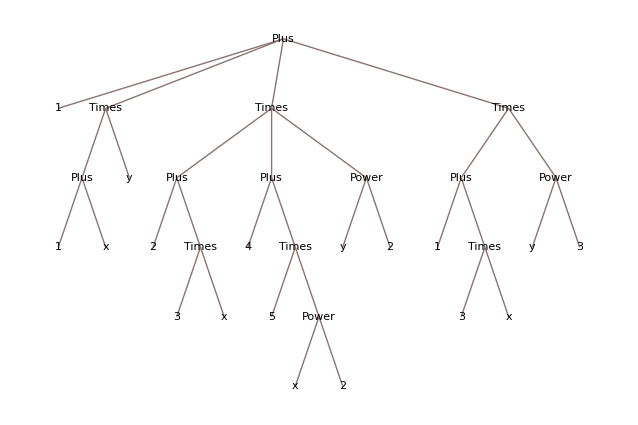

```mathematica
TreeForm[1+y(1+x)+y^2(2+3x)(4+5x^2)+y^3(1+3x)]
```

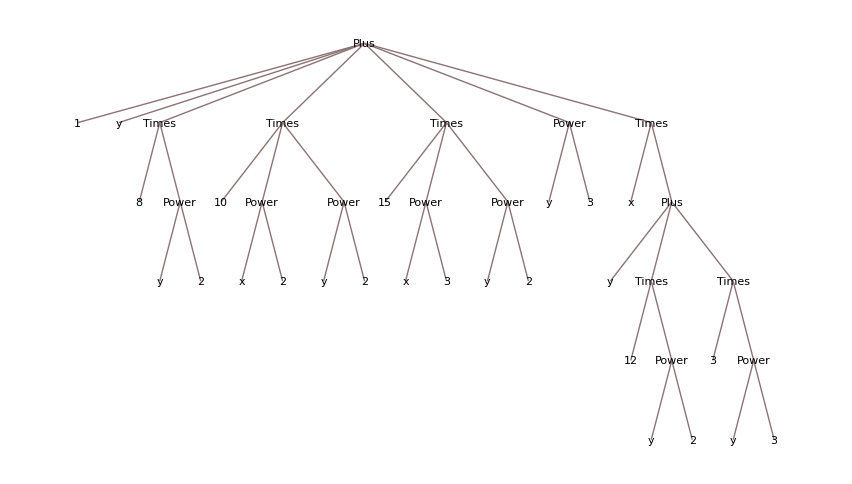

```mathematica
TreeForm[Collect[1+y(1+x)+y^2(2+3x)(4+5x^2)+y^3(1+3x),x]]
```